# Green’s Function

### Author

Eric W. Weisstein
June 2, 2014

This notebook downloaded from http://mathworld.wolfram.com/notebooks/DifferentialEquations/GreensFunction.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/GreensFunction.html.

©2014 Wolfram Research, Inc. except for portions noted otherwise

## Figures

### Point Displacement

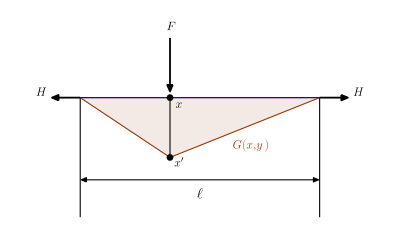

### Example Function

```mathematica
e=4;
Plot3D[(1/(4π*e))*(1/If[x==y,Indeterminate,Abs[x-y]]),
{x,-10,10},{y,-10,10},ColorFunction->Function[{x,y,z},Hue[z]],Mesh->15,FaceGrids->{{0,0,1},{0,0,-1}},FaceGridsStyle->Directive[Gray,Dashed],AxesLabel->{x,y},Ticks->{{-10,0,10},{-10,0,10},{}},ImageSize->400]
```

-Graphics3D-